# Lecture 3 : A conceptual introduction to data pre - processing.

```mathematica
Murilo da Silva Baptista
murilo.baptista@abdn.ac.uk
```

[Lecture based on your textbook “A Hands-On Introduction to Data Science”]

In the real world data can be “dirty” (incomplete, noisy, inconsistent) and needs to be “cleaned”

Incomplete: attribute values lacking

Noisy: outliers due to random fluctuations or real extreme events due to natural sources

Inconsistent: data contains discrepancies in codes or names. For example, “name” column does not contains alphabetical letters.     .00

Garbage in, Garbage out principle: messy data will yield messy analytical models.

N. H. Son, Link

```mathematica
http://www.mimuw.edu.pl/~son/datamining/DM/4-preprocess.pdf
```

# Structure of next slides

Data Cleaning

Data Integration

Data Transformation

Data Reduction

Data Discretization

# Data Cleaning

Data Munging (wrangling): often the data is not in a format that is easy to work with. Thus we need to convert it to something more suitable for the analysis to be performed, or tailored to the model to be applied to the data.

Metadata: data with different fields, binary, floating, nominal, texts, images, sound, etc... Learn to recognize what you want for extraction.

reconstructed/handling missing information

Smooth noisy data

Fill in missing values, smooth noisy data, identify or remove outliers, and resolve inconsistencies

Manipulate the data (wrangling or munging) to turn into something more convenient, useful

consider the following BBC pizza dough recipe Link:

“Put 300g strong bread flour, 1 tsp instant yeast, 1 tsp of salt, 1 tbsp of olive oil into a large bowl, with 200ml warm water and knead for 5 mins until smooth.”

Manually or automatically one needs to identify items

"Put 300g strong bread flour, 1tsp instant yeast, 1tsp of salt, 1tbsp of olive oil into a large bowl, with 200ml warm water and knead for 5mins until smooth."

and create the data table

```mathematica
Dough ={{"Ingredients", "Quantity","Units"},{"Strong bread flour",300, "g"},{"Instant yeast",1, "tsp"},{"Salt",1, "tsp"},{"Olive oil",1, "tbsp"},{"Warm water",200,"ml"}} //Dataset
```

Units can mean a standard Physical Unit or a measure (tsb)!

From the Wrangled data alone, original information might not be recovered.

Physical units can be introduced using Quantity[element, “unit”], or directly using CTRL=

```mathematica
Quantity[30,"Grams"]
```

30 g

```mathematica
Quantity[{10, 210},"Grams"]
```

{10 g,210 g}

Mathematica understands "tsb" as unit but not "lalalala"

Data might be missing due to

Information required not existing: “Can you please tell the date you first bought a Lamborghini?”

For the SDGs data, countries provide not all the indicators for each target and each goal. Countries also provide for one year data, but not for another year.

For the CHARLS survey data, information on income is either unavailable or unreliable. This is reconstructed from expenses.

process of collecting it: information not required at the time, information not known or available at the time of the collection

equipment malfunction

Ignoring that record

using a global constant to fill it in

Imputation (e.g. averages, maximal values, minimal values, local averages)

Modelling the data

Suppose the following dataset, with empty cells  recognized as such by Mathematica by Missing[“NotAvailable”]

```mathematica
nRows=10;  (*Number of rows*)

(*Generate data for columns*)
data=Table[Module[{xChoice,yChoice},xChoice=RandomChoice[{0.8,0.2}-> {RandomReal[10],Missing["NotAvailable"]}];
yChoice=RandomChoice[{0.8,0.2}-> {RandomReal[10],Missing["NotAvailable"]}];
<|"PrimaryKey"->i,"VariableX"->xChoice,"VariableY"->yChoice|>],{i,nRows}];

(*Create the dataset*)
dataset=Dataset[data];

(*Display the dataset*)
dataset
```

```mathematica
Select[Normal@dataset,#VariableX=!=Missing["NotAvailable"]&][[All,"VariableX"]]
```

{1.96974,1.65878,5.85998,1.76998,9.4603,4.06916,6.85549,0.246288,5.57803}

Knowing that numbers had a uniform random distribution, it makes sense to replace missing (either "" or Missing["NotAvailable"]) by the average in the column

```mathematica
(*Calculate the average values of each column*)averageX=Mean@Select[Normal@dataset,#VariableX=!=Missing["NotAvailable"]&][[All,"VariableX"]];
averageY=Mean@Select[Normal@dataset,#VariableY=!=Missing["NotAvailable"]&][[All,"VariableY"]];

(*Replace NA and zero values with the calculated averages*)
cleanedDataset=dataset[All,<|"PrimaryKey"->#PrimaryKey,"VariableX"->If[#VariableX===Missing["NotAvailable"],averageX,#VariableX],"VariableY"->If[#VariableY===Missing["NotAvailable"],averageY,#VariableY]|>&];

(*cleaned dataset*)
cleanedDataset
```

Dates are presented in several different styles, and you will need to choose one style.

We will work much to handle dates, but good to know that Mathematica can deal with many forms of entries, and can create objects that are identified by a calendar date, actually many types of calendars, and time systems (UTI, UTC (or GMT), ECT...) (introduced in Mathematica 13.0).

```mathematica
DateObject[{2022,10,1,0,0,0},TimeSystem->"UTC",TimeZone->0]
```

Sat 1 Oct 2022 00:00:00UTC

local time adopted :

```mathematica
DateObject[{2021,1,20,0,0,0}]
```

Wed 20 Jan 2021 00:00:00GMT

```mathematica
DateObject[]
```

Fri 6 Feb 2026 15:06:45GMT

We can also discretize the dates into weeks or months:

```mathematica
DateObject[%,"Week"]
DateObject[%,"Month"]
```

Week beginning: Mon 2 Feb 2026

Feb 2026

Mathematica has its own Absolute Date format

```mathematica
AbsoluteTime[]
```

3.979379289651341×10^9

gives the total number of seconds since the beginning of January 1, 1900, in your time zone .

```mathematica
DateObject[]
```

Tue 13 Jan 2026 16:25:59GMT

Some tools can deal with nominal values internally

Other methods (neural nets, regression, nearest neighbour) require only numeric inputs

```mathematica
databridge=Import["https://archive.ics.uci.edu/ml/machine-learning-databases/bridges/bridges.data.version1", "Data"];
```

```mathematica
databridge[[1;;30]]//Dataset
```

```mathematica
databridge[[All,11]]=databridge[[All,11]]/."SHORT"-> 1;
databridge[[All,11]]=databridge[[All,11]]/."MEDIUM"-> 2;
databridge[[All,11]]=databridge[[All,11]]/."LONG"-> 3;
```

```mathematica
databridge//Dataset
```

The coding could be a bit more elaborated :

```mathematica
databridge=Import["https://archive.ics.uci.edu/ml/machine-learning-databases/bridges/bridges.data.version1", "Data"];
```

```mathematica
databridge[[All,11]]=Replace[databridge[[All,11]],{"SHORT"-> 1,"MEDIUM"-> 2,"LONG"-> 3},{1} ];
databridge//Dataset
```

A simple encoding: transforming categorical variables into discrete numbers, for example “female”->0 and “male”->1, or education level (“PhD”, “Master”, “higher”, “secondary”, “primary”, “no education”)->(5,4,3,2,1,0).

Numbers (numeric marks) can be converted to ordered attributes (e . g . CGS) preserving natural order :

Data may be corrupted due to :

Faulty instrument

data entry

technology limitations (sensor ranges)

start with outliers

check for wrong spelling

check for impossible data (Temperature in Aberdeen : +240∘C)

Model (regression) the data and consider deviations as corrupted data

Let us get the Global Monthly Temperatures

Original data:

```mathematica
tempdata=Import["https://data.giss.nasa.gov/gistemp/tabledata_v4/GLB.Ts+dSST.csv","Data"]
```

{{Year,Jan,Feb,Mar,Apr,May,Jun,Jul,Aug,Sep,Oct,Nov,Dec,J-D,D-N,DJF,MAM,JJA,SON},{1880,-0.19,-0.25,-0.1,-0.17,-0.11,-0.22,-0.19,-0.11,-0.15,-0.24,-0.23,-0.18,-0.18,***,***,-0.13,-0.17,-0.21},{1881,-0.2,-0.15,0.03,0.04,0.05,-0.19,0.,-0.04,-0.16,-0.22,-0.19,-0.07,-0.09,-.10,-.18,0.04,-0.08,-0.19},{1882,0.15,0.13,0.04,-0.17,-0.15,-0.23,-0.17,-0.08,-0.15,-0.24,-0.17,-0.36,-0.12,-.09,.07,-0.09,-0.16,-0.19},{1883,-0.3,-0.37,-0.13,-0.18,-0.17,-0.08,-0.07,-0.14,-0.21,-0.11,-0.23,-0.11,-0.18,-.20,-.34,-0.16,-0.1,-0.19},{1884,-0.13,-0.08,-0.36,-0.41,-0.34,-0.36,-0.3,-0.27,-0.27,-0.25,-0.34,-0.31,-0.29,-.27,-.11,-0.37,-0.31,-0.29},{1885,-0.59,-0.34,-0.27,-0.42,-0.46,-0.44,-0.34,-0.32,-0.29,-0.24,-0.24,-0.11,-0.34,-.35,-.41,-0.38,-0.37,-0.26},{1886,-0.44,-0.51,-0.43,-0.29,-0.25,-0.35,-0.19,-0.31,-0.24,-0.28,-0.28,-0.25,-0.32,-.31,-.36,-0.32,-0.28,-0.27},{1887,-0.73,-0.58,-0.36,-0.36,-0.31,-0.25,-0.26,-0.36,-0.26,-0.36,-0.26,-0.34,-0.37,-.36,-.52,-0.34,-0.29,-0.29},{1888,-0.34,-0.36,-0.41,-0.21,-0.22,-0.17,-0.11,-0.16,-0.12,0.01,0.02,-0.05,-0.18,-.20,-.35,-0.28,-0.15,-0.03},{1889,-0.1,0.16,0.06,0.09,-0.01,-0.1,-0.07,-0.2,-0.24,-0.26,-0.34,-0.3,-0.11,-.09,.01,0.04,-0.13,-0.28},{1890,-0.43,-0.45,-0.41,-0.3,-0.4,-0.25,-0.28,-0.39,-0.37,-0.25,-0.44,-0.32,-0.36,-.36,-.39,-0.37,-0.31,-0.35},{1891,-0.34,-0.47,-0.18,-0.28,-0.17,-0.21,-0.18,-0.17,-0.16,-0.22,-0.32,-0.04,-0.23,-.25,-.38,-0.21,-0.19,-0.23},{1892,-0.29,-0.12,-0.4,-0.33,-0.23,-0.22,-0.31,-0.27,-0.17,-0.14,-0.42,-0.39,-0.27,-.25,-.15,-0.32,-0.27,-0.24},{1893,-0.81,-0.56,-0.23,-0.28,-0.34,-0.25,-0.14,-0.25,-0.22,-0.18,-0.19,-0.32,-0.31,-.32,-.59,-0.28,-0.21,-0.2},{1894,-0.53,-0.3,-0.24,-0.46,-0.31,-0.41,-0.24,-0.24,-0.28,-0.23,-0.26,-0.22,-0.31,-.32,-.38,-0.34,-0.3,-0.26},{1895,-0.41,-0.43,-0.33,-0.22,-0.28,-0.21,-0.17,-0.17,-0.12,-0.11,-0.17,-0.15,-0.23,-.24,-.35,-0.28,-0.19,-0.13},{1896,-0.23,-0.13,-0.27,-0.31,-0.16,-0.12,-0.03,-0.06,-0.08,0.06,-0.05,-0.05,-0.12,-.13,-.17,-0.25,-0.07,-0.02},{1897,-0.16,-0.17,-0.14,-0.03,-0.02,-0.12,-0.03,-0.1,-0.09,-0.13,-0.19,-0.21,-0.12,-.10,-.13,-0.07,-0.08,-0.14},{1898,-0.04,-0.31,-0.52,-0.31,-0.31,-0.2,-0.23,-0.27,-0.22,-0.35,-0.39,-0.24,-0.28,-.28,-.19,-0.38,-0.23,-0.32},{1899,-0.17,-0.39,-0.36,-0.21,-0.23,-0.32,-0.16,-0.09,-0.06,-0.04,0.12,-0.27,-0.18,-.18,-.27,-0.27,-0.19,0.01},{1900,-0.37,-0.06,0.,-0.1,-0.09,-0.11,-0.14,-0.09,-0.06,0.09,-0.08,-0.08,-0.09,-.11,-.24,-0.07,-0.11,-0.02},{1901,-0.22,-0.11,0.05,-0.03,-0.16,-0.12,-0.15,-0.21,-0.23,-0.29,-0.17,-0.28,-0.16,-.14,-.14,-0.05,-0.16,-0.23},{1902,-0.17,-0.09,-0.28,-0.28,-0.33,-0.32,-0.28,-0.31,-0.29,-0.3,-0.37,-0.43,-0.29,-.27,-.18,-0.3,-0.3,-0.32},{1903,-0.25,-0.07,-0.24,-0.42,-0.4,-0.43,-0.35,-0.46,-0.5,-0.47,-0.42,-0.52,-0.38,-.37,-.25,-0.35,-0.41,-0.46},{1904,-0.64,-0.59,-0.52,-0.51,-0.52,-0.49,-0.52,-0.49,-0.56,-0.39,-0.18,-0.34,-0.48,-.50,-.58,-0.52,-0.5,-0.38},{1905,-0.36,-0.6,-0.22,-0.35,-0.3,-0.29,-0.27,-0.21,-0.19,-0.25,-0.08,-0.14,-0.27,-.29,-.43,-0.29,-0.25,-0.17},{1906,-0.29,-0.3,-0.19,-0.06,-0.26,-0.2,-0.23,-0.2,-0.28,-0.21,-0.38,-0.15,-0.23,-.23,-.24,-0.17,-0.21,-0.29},{1907,-0.44,-0.52,-0.28,-0.38,-0.47,-0.42,-0.36,-0.35,-0.35,-0.23,-0.47,-0.47,-0.39,-.37,-.37,-0.37,-0.38,-0.35},{1908,-0.45,-0.33,-0.56,-0.45,-0.38,-0.39,-0.36,-0.46,-0.36,-0.44,-0.52,-0.5,-0.43,-.43,-.42,-0.46,-0.4,-0.44},{1909,-0.74,-0.47,-0.55,-0.6,-0.55,-0.52,-0.45,-0.34,-0.39,-0.4,-0.32,-0.57,-0.49,-.48,-.57,-0.57,-0.44,-0.37},{1910,-0.43,-0.42,-0.52,-0.44,-0.35,-0.39,-0.35,-0.37,-0.39,-0.42,-0.57,-0.68,-0.44,-.43,-.47,-0.43,-0.37,-0.46},{1911,-0.62,-0.58,-0.61,-0.54,-0.52,-0.51,-0.43,-0.44,-0.41,-0.26,-0.21,-0.22,-0.45,-.48,-.63,-0.56,-0.46,-0.3},{1912,-0.26,-0.15,-0.38,-0.18,-0.22,-0.24,-0.43,-0.55,-0.58,-0.58,-0.4,-0.44,-0.37,-.35,-.21,-0.26,-0.41,-0.52},{1913,-0.41,-0.46,-0.43,-0.41,-0.45,-0.46,-0.37,-0.34,-0.35,-0.33,-0.2,-0.03,-0.35,-.39,-.44,-0.43,-0.39,-0.29},{1914,0.04,-0.1,-0.25,-0.3,-0.22,-0.26,-0.24,-0.17,-0.17,-0.04,-0.16,-0.05,-0.16,-.16,-.03,-0.26,-0.22,-0.12},{1915,-0.21,-0.04,-0.1,0.06,-0.06,-0.22,-0.12,-0.22,-0.2,-0.25,-0.13,-0.21,-0.14,-.13,-.10,-0.03,-0.19,-0.19},{1916,-0.13,-0.16,-0.29,-0.31,-0.36,-0.49,-0.37,-0.28,-0.36,-0.33,-0.47,-0.82,-0.36,-.31,-.17,-0.32,-0.38,-0.39},{1917,-0.57,-0.63,-0.64,-0.55,-0.56,-0.44,-0.26,-0.22,-0.23,-0.44,-0.34,-0.68,-0.46,-.48,-.68,-0.58,-0.31,-0.34},{1918,-0.48,-0.35,-0.25,-0.45,-0.44,-0.37,-0.32,-0.32,-0.17,-0.06,-0.12,-0.3,-0.3,-.33,-.50,-0.38,-0.34,-0.12},{1919,-0.2,-0.23,-0.22,-0.13,-0.28,-0.36,-0.29,-0.33,-0.25,-0.21,-0.42,-0.43,-0.28,-.27,-.24,-0.21,-0.33,-0.29},{1920,-0.25,-0.27,-0.12,-0.25,-0.27,-0.36,-0.3,-0.26,-0.22,-0.26,-0.27,-0.47,-0.28,-.27,-.32,-0.21,-0.31,-0.25},{1921,-0.05,-0.18,-0.23,-0.3,-0.31,-0.27,-0.15,-0.27,-0.19,-0.04,-0.15,-0.18,-0.19,-.22,-.23,-0.28,-0.23,-0.13},{1922,-0.34,-0.45,-0.15,-0.23,-0.33,-0.31,-0.27,-0.33,-0.35,-0.32,-0.14,-0.2,-0.29,-.28,-.32,-0.24,-0.3,-0.27},{1923,-0.27,-0.4,-0.34,-0.41,-0.34,-0.3,-0.31,-0.34,-0.31,-0.14,-0.03,-0.04,-0.27,-.28,-.29,-0.36,-0.31,-0.16},{1924,-0.23,-0.23,-0.09,-0.31,-0.19,-0.27,-0.29,-0.36,-0.32,-0.35,-0.21,-0.44,-0.27,-.24,-.17,-0.19,-0.31,-0.29},{1925,-0.38,-0.39,-0.28,-0.26,-0.3,-0.33,-0.27,-0.21,-0.2,-0.18,0.05,0.06,-0.22,-.27,-.40,-0.28,-0.27,-0.11},{1926,0.2,0.02,0.11,-0.14,-0.24,-0.27,-0.28,-0.13,-0.15,-0.11,-0.07,-0.3,-0.11,-.08,.09,-0.09,-0.23,-0.11},{1927,-0.28,-0.18,-0.39,-0.31,-0.26,-0.28,-0.19,-0.24,-0.13,-0.01,-0.06,-0.33,-0.22,-.22,-.25,-0.32,-0.24,-0.07},{1928,-0.03,-0.1,-0.25,-0.29,-0.3,-0.39,-0.2,-0.23,-0.22,-0.19,-0.1,-0.17,-0.2,-.22,-.15,-0.28,-0.27,-0.17},{1929,-0.45,-0.59,-0.33,-0.42,-0.38,-0.44,-0.37,-0.33,-0.26,-0.15,-0.12,-0.55,-0.36,-.33,-.40,-0.38,-0.38,-0.17},{1930,-0.31,-0.27,-0.11,-0.25,-0.24,-0.22,-0.22,-0.15,-0.16,-0.12,0.17,-0.06,-0.16,-.20,-.38,-0.2,-0.2,-0.04},{1931,-0.11,-0.21,-0.11,-0.23,-0.2,-0.08,-0.04,-0.04,-0.07,0.06,-0.06,-0.05,-0.09,-.10,-.13,-0.18,-0.05,-0.02},{1932,0.15,-0.18,-0.18,-0.06,-0.18,-0.29,-0.25,-0.22,-0.1,-0.09,-0.28,-0.27,-0.16,-.14,-.03,-0.14,-0.25,-0.16},{1933,-0.24,-0.3,-0.3,-0.25,-0.29,-0.34,-0.21,-0.23,-0.29,-0.25,-0.31,-0.45,-0.29,-.27,-.27,-0.28,-0.26,-0.28},{1934,-0.21,-0.03,-0.29,-0.3,-0.09,-0.15,-0.1,-0.12,-0.15,-0.06,0.03,-0.03,-0.13,-.16,-.23,-0.23,-0.13,-0.06},{1935,-0.34,0.14,-0.14,-0.38,-0.29,-0.27,-0.22,-0.22,-0.21,-0.06,-0.26,-0.17,-0.2,-.19,-.08,-0.27,-0.23,-0.18},{1936,-0.28,-0.38,-0.21,-0.2,-0.16,-0.22,-0.1,-0.14,-0.09,-0.03,0.01,-0.01,-0.15,-.16,-.28,-0.19,-0.15,-0.04},{1937,-0.07,0.03,-0.21,-0.16,-0.06,-0.05,-0.03,0.01,0.09,0.09,0.08,-0.08,-0.03,-.02,-.02,-0.14,-0.02,0.08},{1938,0.08,0.04,0.09,0.06,-0.1,-0.17,-0.09,-0.05,0.01,0.15,0.07,-0.13,0.,.00,.01,0.02,-0.11,0.08},{1939,-0.05,-0.07,-0.18,-0.11,-0.04,-0.07,-0.06,-0.06,-0.07,-0.04,0.07,0.42,-0.02,-.07,-.08,-0.11,-0.06,-0.02},{1940,-0.01,0.08,0.09,0.17,0.1,0.11,0.12,0.06,0.15,0.1,0.16,0.31,0.12,.13,.16,0.12,0.1,0.14},{1941,0.17,0.3,0.1,0.16,0.16,0.13,0.22,0.14,0.02,0.35,0.22,0.21,0.18,.19,.26,0.14,0.16,0.2},{1942,0.29,0.02,0.05,0.09,0.1,0.04,0.,-0.04,-0.03,0.01,0.09,0.12,0.06,.07,.17,0.08,0.,0.02},{1943,-0.01,0.17,-0.04,0.1,0.06,-0.06,0.08,0.,0.05,0.23,0.19,0.23,0.08,.07,.09,0.04,0.01,0.16},{1944,0.35,0.24,0.26,0.19,0.18,0.15,0.17,0.18,0.28,0.26,0.11,0.04,0.2,.22,.27,0.21,0.17,0.22},{1945,0.1,0.01,0.06,0.19,0.06,0.,0.04,0.26,0.2,0.18,0.06,-0.07,0.09,.10,.05,0.1,0.1,0.15},{1946,0.15,0.02,0.01,0.05,-0.07,-0.21,-0.12,-0.2,-0.08,-0.08,-0.06,-0.31,-0.08,-.06,.03,0.,-0.18,-0.07},{1947,-0.07,-0.08,0.06,0.06,-0.02,-0.02,-0.04,-0.07,-0.13,0.07,0.02,-0.14,-0.03,-.04,-.15,0.03,-0.04,-0.01},{1948,0.06,-0.15,-0.24,-0.12,-0.01,-0.05,-0.11,-0.12,-0.14,-0.05,-0.13,-0.24,-0.11,-.10,-.07,-0.12,-0.09,-0.11},{1949,0.06,-0.15,-0.02,-0.11,-0.1,-0.27,-0.13,-0.13,-0.14,-0.07,-0.1,-0.18,-0.11,-.12,-.11,-0.08,-0.18,-0.1},{1950,-0.26,-0.27,-0.08,-0.21,-0.11,-0.05,-0.09,-0.16,-0.11,-0.2,-0.34,-0.22,-0.18,-.17,-.24,-0.13,-0.1,-0.22},{1951,-0.34,-0.41,-0.2,-0.14,0.,-0.06,-0.01,0.06,0.05,0.08,-0.01,0.16,-0.07,-.10,-.33,-0.12,-0.01,0.04},{1952,0.11,0.11,-0.08,0.03,-0.03,-0.03,0.04,0.05,0.07,0.,-0.13,-0.02,0.01,.03,.13,-0.03,0.02,-0.02},{1953,0.07,0.15,0.11,0.19,0.11,0.12,0.01,0.05,0.04,0.08,-0.03,0.05,0.08,.08,.07,0.14,0.06,0.03},{1954,-0.24,-0.1,-0.15,-0.14,-0.2,-0.18,-0.19,-0.17,-0.1,-0.02,0.08,-0.18,-0.13,-.11,-.10,-0.16,-0.18,-0.01},{1955,0.14,-0.16,-0.32,-0.22,-0.2,-0.13,-0.11,0.02,-0.11,-0.05,-0.25,-0.28,-0.14,-.13,-.07,-0.25,-0.07,-0.14},{1956,-0.13,-0.24,-0.21,-0.28,-0.29,-0.15,-0.09,-0.25,-0.19,-0.23,-0.15,-0.06,-0.19,-.21,-.22,-0.26,-0.17,-0.19},{1957,-0.09,-0.03,-0.05,0.,0.09,0.15,0.02,0.15,0.08,0.01,0.08,0.15,0.05,.03,-.06,0.01,0.11,0.06},{1958,0.39,0.22,0.09,0.02,0.06,-0.09,0.05,-0.05,-0.03,0.04,0.02,0.01,0.06,.07,.25,0.05,-0.03,0.01},{1959,0.08,0.07,0.18,0.16,0.04,0.03,0.03,-0.01,-0.06,-0.07,-0.08,0.,0.03,.03,.05,0.12,0.02,-0.07},{1960,0.,0.13,-0.35,-0.15,-0.08,-0.04,-0.04,0.02,0.07,0.06,-0.11,0.19,-0.03,-.04,.04,-0.19,-0.02,0.},{1961,0.07,0.19,0.09,0.13,0.12,0.12,0.01,0.01,0.08,0.,0.03,-0.17,0.06,.09,.15,0.12,0.04,0.04},{1962,0.05,0.15,0.1,0.05,-0.06,0.03,0.02,-0.01,0.,0.01,0.06,-0.03,0.03,.02,.01,0.03,0.01,0.02},{1963,-0.03,0.18,-0.14,-0.07,-0.06,0.05,0.06,0.22,0.17,0.14,0.15,-0.03,0.05,.05,.04,-0.09,0.11,0.15},{1964,-0.09,-0.1,-0.21,-0.32,-0.25,-0.04,-0.04,-0.22,-0.29,-0.31,-0.21,-0.3,-0.2,-.18,-.07,-0.26,-0.1,-0.27},{1965,-0.08,-0.17,-0.13,-0.19,-0.12,-0.08,-0.13,-0.04,-0.15,-0.05,-0.06,-0.08,-0.11,-.13,-.18,-0.15,-0.09,-0.09},{1966,-0.19,-0.04,0.04,-0.13,-0.12,0.01,0.08,-0.09,-0.03,-0.17,-0.01,-0.02,-0.06,-.06,-.10,-0.07,0.,-0.07},{1967,-0.08,-0.21,0.05,-0.05,0.12,-0.08,0.02,0.01,-0.06,0.09,-0.05,-0.05,-0.02,-.02,-.10,0.04,-0.02,-0.01},{1968,-0.26,-0.14,0.2,-0.06,-0.14,-0.09,-0.13,-0.09,-0.19,0.09,-0.05,-0.15,-0.08,-.07,-.15,0.,-0.1,-0.05},{1969,-0.11,-0.18,0.01,0.17,0.18,0.03,-0.05,0.04,0.08,0.09,0.12,0.25,0.05,.02,-.14,0.12,0.01,0.1},{1970,0.08,0.22,0.06,0.05,-0.03,-0.02,0.02,-0.1,0.12,0.03,0.02,-0.12,0.03,.06,.18,0.03,-0.04,0.06},{1971,-0.02,-0.15,-0.18,-0.07,-0.05,-0.16,-0.07,-0.01,-0.05,-0.04,-0.07,-0.08,-0.08,-.08,-.10,-0.1,-0.08,-0.06},{1972,-0.22,-0.18,0.02,0.,-0.03,0.04,0.01,0.16,0.02,0.08,0.02,0.18,0.01,-.01,-.16,0.,0.07,0.04},{1973,0.29,0.32,0.29,0.27,0.23,0.19,0.13,0.05,0.09,0.1,0.04,-0.07,0.16,.18,.26,0.26,0.12,0.08},{1974,-0.1,-0.27,-0.05,-0.11,-0.04,-0.05,-0.03,0.1,-0.08,-0.06,-0.08,-0.08,-0.07,-.07,-.14,-0.07,0.01,-0.07},{1975,0.1,0.08,0.12,0.04,0.16,-0.01,-0.01,-0.17,-0.02,-0.11,-0.17,-0.17,-0.01,-.01,.03,0.11,-0.06,-0.1},{1976,-0.03,-0.06,-0.21,-0.07,-0.2,-0.12,-0.1,-0.12,-0.07,-0.24,-0.06,0.11,-0.1,-.12,-.09,-0.16,-0.11,-0.12},{1977,0.18,0.23,0.24,0.26,0.33,0.27,0.2,0.18,0.02,0.03,0.16,0.03,0.18,.18,.17,0.28,0.22,0.07},{1978,0.06,0.1,0.19,0.17,0.09,-0.01,0.04,-0.14,0.06,0.03,0.13,0.08,0.07,.06,.06,0.15,-0.04,0.07},{1979,0.08,-0.1,0.19,0.15,0.03,0.14,0.04,0.17,0.25,0.26,0.28,0.48,0.16,.13,.02,0.13,0.11,0.26},{1980,0.29,0.39,0.29,0.3,0.35,0.2,0.22,0.18,0.2,0.13,0.29,0.21,0.26,.28,.39,0.31,0.2,0.21},{1981,0.53,0.42,0.48,0.32,0.24,0.29,0.32,0.35,0.14,0.12,0.23,0.41,0.32,.30,.39,0.35,0.32,0.16},{1982,0.05,0.15,0.03,0.15,0.18,0.05,0.14,0.03,0.14,0.13,0.18,0.42,0.14,.14,.20,0.12,0.08,0.15},{1983,0.53,0.43,0.42,0.27,0.34,0.22,0.18,0.36,0.37,0.17,0.3,0.16,0.31,.33,.46,0.34,0.25,0.28},{1984,0.31,0.14,0.26,0.06,0.33,0.02,0.19,0.19,0.21,0.13,0.06,-0.04,0.16,.17,.20,0.22,0.14,0.14},{1985,0.22,-0.04,0.17,0.12,0.14,0.15,0.04,0.17,0.13,0.12,0.05,0.14,0.12,.10,.05,0.15,0.12,0.1},{1986,0.26,0.37,0.3,0.22,0.21,0.12,0.11,0.16,0.03,0.15,0.1,0.13,0.18,.18,.26,0.24,0.13,0.09},{1987,0.32,0.43,0.18,0.24,0.25,0.35,0.4,0.25,0.35,0.33,0.29,0.46,0.32,.29,.29,0.23,0.33,0.32},{1988,0.57,0.44,0.52,0.43,0.44,0.4,0.33,0.39,0.37,0.38,0.12,0.29,0.39,.40,.49,0.46,0.37,0.29},{1989,0.12,0.3,0.36,0.29,0.17,0.17,0.34,0.33,0.34,0.29,0.2,0.37,0.27,.27,.24,0.27,0.28,0.28},{1990,0.41,0.44,0.8,0.56,0.45,0.37,0.46,0.34,0.23,0.45,0.46,0.41,0.45,.45,.41,0.61,0.39,0.38},{1991,0.43,0.5,0.36,0.51,0.34,0.53,0.48,0.39,0.44,0.29,0.3,0.32,0.41,.41,.44,0.4,0.47,0.34},{1992,0.48,0.4,0.48,0.27,0.31,0.26,0.09,0.08,-0.01,0.07,0.03,0.22,0.22,.23,.40,0.36,0.14,0.03},{1993,0.34,0.37,0.36,0.28,0.28,0.23,0.25,0.11,0.11,0.23,0.04,0.18,0.23,.24,.31,0.31,0.2,0.13},{1994,0.26,0.02,0.29,0.42,0.28,0.43,0.3,0.21,0.31,0.43,0.44,0.39,0.32,.30,.15,0.33,0.32,0.39},{1995,0.52,0.79,0.47,0.47,0.27,0.43,0.45,0.45,0.33,0.46,0.45,0.26,0.45,.46,.57,0.4,0.45,0.41},{1996,0.24,0.46,0.33,0.33,0.27,0.25,0.37,0.48,0.25,0.22,0.42,0.37,0.33,.32,.32,0.31,0.37,0.3},{1997,0.32,0.41,0.52,0.34,0.35,0.55,0.34,0.41,0.52,0.61,0.64,0.59,0.47,.45,.37,0.4,0.43,0.59},{1998,0.58,0.88,0.63,0.64,0.68,0.77,0.66,0.65,0.42,0.42,0.43,0.55,0.61,.61,.68,0.65,0.69,0.42},{1999,0.48,0.64,0.32,0.32,0.26,0.36,0.38,0.32,0.39,0.34,0.37,0.41,0.38,.39,.56,0.3,0.35,0.37},{2000,0.25,0.56,0.55,0.56,0.36,0.4,0.39,0.42,0.39,0.27,0.3,0.28,0.39,.40,.40,0.49,0.4,0.32},{2001,0.45,0.44,0.55,0.5,0.57,0.52,0.59,0.49,0.52,0.5,0.72,0.55,0.53,.51,.39,0.54,0.53,0.58},{2002,0.77,0.78,0.88,0.58,0.64,0.53,0.62,0.54,0.64,0.54,0.59,0.44,0.63,.64,.70,0.7,0.56,0.59},{2003,0.74,0.58,0.6,0.55,0.61,0.48,0.58,0.64,0.62,0.72,0.53,0.75,0.62,.59,.59,0.59,0.57,0.62},{2004,0.58,0.73,0.63,0.61,0.37,0.44,0.26,0.45,0.5,0.61,0.73,0.5,0.53,.55,.68,0.54,0.38,0.61},{2005,0.75,0.6,0.74,0.67,0.63,0.65,0.61,0.6,0.72,0.76,0.74,0.68,0.68,.66,.62,0.68,0.62,0.74},{2006,0.56,0.74,0.63,0.47,0.48,0.66,0.54,0.71,0.66,0.71,0.74,0.79,0.64,.63,.66,0.53,0.64,0.7},{2007,1.02,0.7,0.72,0.76,0.69,0.61,0.6,0.6,0.61,0.59,0.59,0.5,0.67,.69,.84,0.72,0.6,0.6},{2008,0.3,0.38,0.75,0.54,0.5,0.49,0.6,0.46,0.61,0.67,0.7,0.54,0.54,.54,.39,0.6,0.52,0.66},{2009,0.65,0.53,0.53,0.61,0.66,0.64,0.74,0.69,0.72,0.65,0.8,0.67,0.66,.65,.57,0.6,0.69,0.72},{2010,0.75,0.84,0.92,0.85,0.76,0.68,0.63,0.67,0.63,0.71,0.82,0.45,0.73,.74,.75,0.84,0.66,0.72},{2011,0.52,0.48,0.66,0.64,0.53,0.63,0.7,0.75,0.56,0.65,0.59,0.6,0.61,.60,.48,0.61,0.69,0.6},{2012,0.47,0.48,0.57,0.73,0.78,0.65,0.59,0.66,0.72,0.8,0.78,0.53,0.65,.65,.52,0.69,0.63,0.77},{2013,0.71,0.62,0.67,0.53,0.6,0.7,0.6,0.71,0.77,0.69,0.83,0.7,0.68,.66,.62,0.6,0.67,0.77},{2014,0.77,0.55,0.78,0.81,0.87,0.67,0.58,0.84,0.88,0.8,0.67,0.79,0.75,.74,.67,0.82,0.7,0.79},{2015,0.87,0.91,0.96,0.75,0.8,0.81,0.73,0.8,0.84,1.08,1.06,1.17,0.9,.87,.86,0.84,0.78,0.99},{2016,1.18,1.37,1.35,1.09,0.96,0.81,0.85,1.02,0.9,0.87,0.91,0.86,1.01,1.04,1.24,1.14,0.89,0.9},{2017,1.02,1.14,1.17,0.94,0.91,0.71,0.82,0.88,0.74,0.89,0.87,0.93,0.92,.91,1.01,1.01,0.8,0.83},{2018,0.82,0.85,0.88,0.89,0.81,0.77,0.84,0.78,0.8,1.02,0.83,0.93,0.85,.85,.87,0.86,0.79,0.89},{2019,0.93,0.96,1.17,1.01,0.86,0.9,0.94,0.95,0.93,1.,0.99,1.12,0.98,.96,.94,1.01,0.93,0.97},{2020,1.18,1.24,1.18,1.12,0.99,0.91,0.89,0.86,0.97,0.87,1.09,0.8,1.01,1.03,1.18,1.1,0.89,0.97},{2021,0.81,0.64,0.89,0.76,0.79,0.85,0.92,0.81,0.93,0.99,0.93,0.87,0.85,.84,.75,0.81,0.86,0.95},{2022,0.91,0.89,1.05,0.84,0.84,0.92,0.94,0.95,0.89,0.97,0.73,0.8,0.89,.90,.89,0.91,0.94,0.86},{2023,0.88,0.97,1.23,0.99,0.94,1.09,1.2,1.19,1.48,1.34,1.4,1.37,1.17,1.13,.88,1.05,1.16,1.41},{2024,1.25,1.44,1.39,1.31,1.15,1.2,1.2,1.29,1.24,1.33,1.3,1.27,1.28,1.29,1.36,1.28,1.23,1.29},{2025,1.38,1.26,1.36,1.23,1.08,1.05,1.02,1.16,1.25,1.19,1.21,1.05,1.19,1.21,1.30,1.22,1.08,1.22}}

I will however get the curated Wolfram data:

```mathematica
tempdata=ResourceData[ResourceObject["NASA GISTEMP Global Means"]]
```

Let me get the annual mean temperature

```mathematica
annualTempMeans=tempdata[[21;;136,{1,14}]]
```

```mathematica
Normal[annualTempMeans];
```

```mathematica
tempdata[[21,1]]
```

Year: 1900

```mathematica
Values[tempdata[[21;;136,2;;13]]];
```

transform  Dataset  to  List of Associations:

```mathematica
Normal[tempdata[[21;;136,2;;13]]]
```

Extract the values and put them in a list:

```mathematica
Normal[Values[tempdata[[21;;136,2;;13]]]];
```

The average could be calculated by (manipulation bellow Normal[Values[ extracts the values of the data in a datasetformat)

```mathematica
annualTMeans=ArrayReduce[Mean,Normal[Values[tempdata[[21;;136,2;;13]]]],2]
```

{-0.0833333 _Δ^◦C,-0.140833 _Δ^◦C,-0.263333 _Δ^◦C,-0.346667 _Δ^◦C,-0.436667 _Δ^◦C,-0.2675 _Δ^◦C,-0.214167 _Δ^◦C,-0.390833 _Δ^◦C,-0.424167 _Δ^◦C,-0.468333 _Δ^◦C,-0.418333 _Δ^◦C,-0.436667 _Δ^◦C,-0.343333 _Δ^◦C,-0.33 _Δ^◦C,-0.151667 _Δ^◦C,-0.105833 _Δ^◦C,-0.335833 _Δ^◦C,-0.4 _Δ^◦C,-0.2525 _Δ^◦C,-0.224167 _Δ^◦C,-0.260833 _Δ^◦C,-0.2075 _Δ^◦C,-0.27 _Δ^◦C,-0.238333 _Δ^◦C,-0.274167 _Δ^◦C,-0.196667 _Δ^◦C,-0.0941667 _Δ^◦C,-0.204167 _Δ^◦C,-0.213333 _Δ^◦C,-0.358333 _Δ^◦C,-0.1375 _Δ^◦C,-0.09 _Δ^◦C,-0.1625 _Δ^◦C,-0.2825 _Δ^◦C,-0.136667 _Δ^◦C,-0.194167 _Δ^◦C,-0.146667 _Δ^◦C,-0.0191667 _Δ^◦C,-0.0216667 _Δ^◦C,-0.025 _Δ^◦C,0.0841667 _Δ^◦C,0.1275 _Δ^◦C,0.0966667 _Δ^◦C,0.1375 _Δ^◦C,0.260833 _Δ^◦C,0.125 _Δ^◦C,-0.0341667 _Δ^◦C,-0.0433333 _Δ^◦C,-0.0908333 _Δ^◦C,-0.0833333 _Δ^◦C,-0.173333 _Δ^◦C,-0.0633333 _Δ^◦C,0.01 _Δ^◦C,0.0766667 _Δ^◦C,-0.118333 _Δ^◦C,-0.1425 _Δ^◦C,-0.196667 _Δ^◦C,0.035 _Δ^◦C,0.0608333 _Δ^◦C,0.0333333 _Δ^◦C,-0.0258333 _Δ^◦C,0.0558333 _Δ^◦C,0.0225 _Δ^◦C,0.0566667 _Δ^◦C,-0.200833 _Δ^◦C,-0.101667 _Δ^◦C,-0.0508333 _Δ^◦C,-0.0225 _Δ^◦C,-0.0691667 _Δ^◦C,0.0666667 _Δ^◦C,0.0275 _Δ^◦C,-0.0925 _Δ^◦C,0.0125 _Δ^◦C,0.151667 _Δ^◦C,-0.0758333 _Δ^◦C,-0.0166667 _Δ^◦C,-0.115 _Δ^◦C,0.181667 _Δ^◦C,0.0641667 _Δ^◦C,0.164167 _Δ^◦C,0.2725 _Δ^◦C,0.324167 _Δ^◦C,0.125 _Δ^◦C,0.301667 _Δ^◦C,0.155 _Δ^◦C,0.113333 _Δ^◦C,0.185833 _Δ^◦C,0.33 _Δ^◦C,0.398333 _Δ^◦C,0.285 _Δ^◦C,0.434167 _Δ^◦C,0.42 _Δ^◦C,0.2225 _Δ^◦C,0.235833 _Δ^◦C,0.3125 _Δ^◦C,0.450833 _Δ^◦C,0.340833 _Δ^◦C,0.474167 _Δ^◦C,0.628333 _Δ^◦C,0.415 _Δ^◦C,0.419167 _Δ^◦C,0.541667 _Δ^◦C,0.624167 _Δ^◦C,0.610833 _Δ^◦C,0.538333 _Δ^◦C,0.681667 _Δ^◦C,0.629167 _Δ^◦C,0.653333 _Δ^◦C,0.528333 _Δ^◦C,0.635833 _Δ^◦C,0.7075 _Δ^◦C,0.593333 _Δ^◦C,0.626667 _Δ^◦C,0.649167 _Δ^◦C,0.739167 _Δ^◦C,0.86 _Δ^◦C}

Let us see inside the Dataset from before using the provided average column:

```mathematica
Head[annualTempMeans]
```

Dataset

```mathematica
Normal[annualTempMeans];
```

Let us plot it :

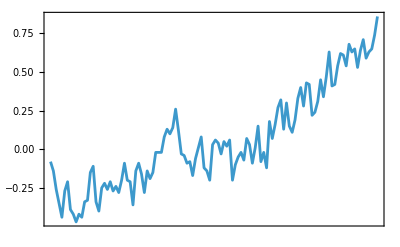

```mathematica
DateListPlot[annualTempMeans]
```

Let us extract the dates from the Dataset object:

```mathematica
yearlist=annualTempMeans[All,1];
```

to extract the year of a date object

```mathematica
FullForm[DateObject[]]
```

DateObject[List[2023,10,4,15,26,2.396574],"Instant","Gregorian",1.]

```mathematica
DateObject[]["Year"]
```

2026

```mathematica
yearlist[[1]]["Year"]
```

1900

Now, to extract the year as a number without the unit (“year”) :

```mathematica
Normal[Table[yearlist[[i]]["Year"],{i,1,Length[yearlist]}]];
```

```mathematica
yearlist=Normal[Table[yearlist[[i]]["Year"],{i,1,Length[yearlist]}]];
```

```mathematica
yearlist;
```

Now the values of the average temperatures (Normal transform Dataset to list, Quantity takes the physical unit out). Normal bellow transforms a dataset object into an association.

```mathematica
Normal[annualTempMeans[All,2]];
```

```mathematica
annualTempMeans[All,2];
```

To  show  annualTempMeans  is  a  Dataset  object  and  we  need  to  use  Normal  to  transform  to  a  list  of  elements, and  not  an  object

```mathematica
Head[annualTempMeans[All,2]];
```

```mathematica
templist=QuantityMagnitude[Normal[annualTempMeans[All,2]]];
```

```mathematica
QuantityMagnitude[Normal[annualTempMeans[All,2]]];
```

```mathematica
{yearlist,templist}//Transpose
```

{{1900,-0.08},{1901,-0.14},{1902,-0.26},{1903,-0.35},{1904,-0.44},{1905,-0.27},{1906,-0.21},{1907,-0.39},{1908,-0.42},{1909,-0.47},{1910,-0.42},{1911,-0.44},{1912,-0.34},{1913,-0.33},{1914,-0.15},{1915,-0.11},{1916,-0.34},{1917,-0.4},{1918,-0.25},{1919,-0.22},{1920,-0.26},{1921,-0.21},{1922,-0.27},{1923,-0.24},{1924,-0.28},{1925,-0.2},{1926,-0.09},{1927,-0.2},{1928,-0.21},{1929,-0.36},{1930,-0.14},{1931,-0.09},{1932,-0.16},{1933,-0.28},{1934,-0.14},{1935,-0.19},{1936,-0.15},{1937,-0.02},{1938,-0.02},{1939,-0.02},{1940,0.08},{1941,0.13},{1942,0.1},{1943,0.14},{1944,0.26},{1945,0.12},{1946,-0.03},{1947,-0.04},{1948,-0.09},{1949,-0.08},{1950,-0.17},{1951,-0.06},{1952,0.01},{1953,0.08},{1954,-0.12},{1955,-0.14},{1956,-0.2},{1957,0.03},{1958,0.06},{1959,0.04},{1960,-0.03},{1961,0.05},{1962,0.02},{1963,0.06},{1964,-0.2},{1965,-0.1},{1966,-0.05},{1967,-0.02},{1968,-0.07},{1969,0.07},{1970,0.03},{1971,-0.09},{1972,0.01},{1973,0.15},{1974,-0.08},{1975,-0.02},{1976,-0.12},{1977,0.18},{1978,0.07},{1979,0.16},{1980,0.27},{1981,0.32},{1982,0.13},{1983,0.3},{1984,0.15},{1985,0.11},{1986,0.19},{1987,0.33},{1988,0.4},{1989,0.28},{1990,0.43},{1991,0.42},{1992,0.22},{1993,0.24},{1994,0.31},{1995,0.45},{1996,0.34},{1997,0.47},{1998,0.63},{1999,0.41},{2000,0.42},{2001,0.54},{2002,0.62},{2003,0.61},{2004,0.54},{2005,0.68},{2006,0.63},{2007,0.65},{2008,0.53},{2009,0.64},{2010,0.71},{2011,0.59},{2012,0.63},{2013,0.65},{2014,0.74},{2015,0.86}}

```mathematica
annualTempMeanslist=Transpose[{yearlist,templist}];
```

```mathematica
templinear=LinearModelFit[annualTempMeanslist,x,x]
```

```mathematica
FittedModel[…]//Normal
```

-16.6712+0.0085475 x

Now let us plot our linear model and do a prediction.

Discuss linear prediction with reality, what is not quite right?

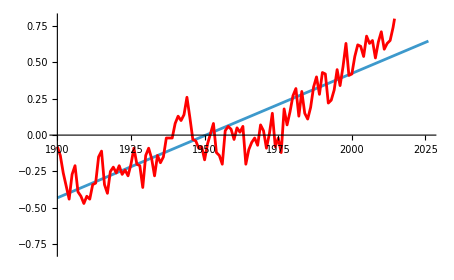

```mathematica
Show[Plot[templinear[x],{x,1900,2026},PlotRange->0.8],DateListPlot[annualTempMeanslist,PlotStyle->Red,PlotRange->0.8]]
```

You would not be able to use ListLinePlot to plot a dataset object, see bellow:

```mathematica
ListLinePlot[annualTempMeans]
```

-Graphics-

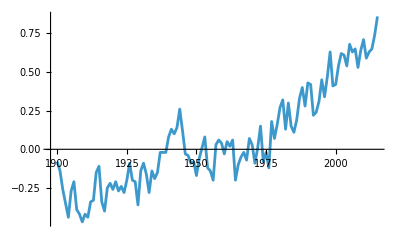

```mathematica
ListLinePlot[annualTempMeanslist]
```

If all you want is to visualize what a fitting would be, without knowledge of the model, use the new function ListFitPlot

```mathematica
ListFitPlot[annualTempMeanslist,PlotFit->"Linear"]
```

-Graphics-

# Data Integration

required for efficient data analysis

Combine data from multiple sources into a coherent storage, file, place.

Detect and resolve data value conflicts

different physical units, scales, metrics...

Address redundant data to integrate different datasets

same attribute with different names (a city may have different names in different datasets from regional or federal government)

Correlation may help to find redundant data, or variables

# Data Transformation

Smoothing: remove noise (stochastic random source) from data

Aggregating: data can be aggregated over a given time period, spatially, or over different groups, to provide statistics such as average, minimum, maximum, sum, and count

summarization :  create a subset (a summary) that represents the most important or relevant information within the original content.

Show Excel file from SDGs in Madagascar, showing the several data for the same year for different gender groups and different age ranges. Data can be found in Myaberdeen for this lecture. Percentages due to different age groups could be combined to represent percentages over the whole population.

Rescaling/normalizing : normalize or rescale data for it to fall into a similar specified range.

v'=(v-min_xa)/(ma x_a - min x_a)

Attribute or feature construction : new attributes constructed from given ones.

from position and times, one can construct velocities and accelerations

Encoding: suppose you want to construct a health index, indicating how healthy an individual is. Also, suppose the candidate was asked about having or not a set of conditions/diseases. For 5 questions, an individual would have answers encoded by the sequence {s_1 = 0, s_2=1,s_3 = 0, s_4 =1,s_5= 1}, where "1" would signify the individual has a condition and “0” otherwise. A health index can be defined using a binary to real conversion by

```mathematica
0 2^{4}+1 2^{3}+0 2^{2}+1 2^{1}+1 2^{0}//N
```

{11.}

```mathematica
11/31//N
```

0.354839

```mathematica
(1 2^{4} + 1 2^{3} + 1 2^{2} + 1 2^{1} + 1 2^{0}) /31//N
```

{1.}

# Data Reduction

Dimensionality reduction

Sampling

Clustering, binning, grouping, gathering, segmenting, etc

The process of finding a reduced representation of the dataset that produces the same or similar analytical results

To produce something much smaller and manageable

For example, eliminating columns/attributes in a dataset, to find optimal features to model.

the selection of a subset (a statistical sample) of individuals from within a statistical population to estimate characteristics of the whole population.

We will cover these topics in great detail later on.

Transform a continuous data into a discrete dataset .

Categorize the data, which may also include binning, grouping, gathering, etc.

example: transform a continuous time-series of temperatures to a daily record of cold, moderate, or hot

#### Working example of a pre-processing : From data about GDP and several CO2 indicators (per capita, trade, etc) for all countries, and for all years, select only the data for Brazil and Germany, and within the period [1990, 2021].

```mathematica
emissionRaw=Import["https://github.com/owid/co2-data/raw/master/owid-co2-data.csv"];
```

```mathematica
emissionRaw[[1;;10,{1,2,4,5,17}]]//TableForm
```

country | year | population | gdp | co2_per_capita
Afghanistan | 1750 | 2802560 | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1751 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1752 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1753 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1754 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1755 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1756 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1757 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1758 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]

Only get data for Country, year, population, GDP, and CO2 per capita (column dimension reduction)

```mathematica
Dimensions[emissionRaw]
```

{50192,79}

```mathematica
emissionReduced1=emissionRaw[[All,{1,2,4,5,17}]];
emissionReduced1[[1;;10]]//TableForm
```

country | year | population | gdp | co2_per_capita
Afghanistan | 1750 | 2802560 | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1751 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1752 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1753 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1754 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1755 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1756 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1757 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
Afghanistan | 1758 | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]

```mathematica
emissionReduced1[[-1]]//TableForm;
```

Now, let us only get data from Brazil and Germany for the period 1990, 2021. Use Cases[expr, pattern]

```mathematica
emissionReducedCountries=Cases[emissionReduced1,{"Brazil"| "Germany",_?(1990<=#<=2021&),___}];
```

___ (BlankNullSequence)—any sequence of zero or more expressions
Notice :

{"Brazil" | "Germany", _?(1990 <= # <= 2021 &), ___}
Matches a list whose : First element = "Brazil" or "Germany"
Second element = a year between 1990 and 2021
Remaining elements = anything (or nothing)

Let us insert the Keys

```mathematica
myKeys=emissionRaw[[1,{1,2,4,5,17}]]
```

{country,year,population,gdp,co2_per_capita}

```mathematica
emissionReducedCountriesKeys=AssociationThread[ToString/@myKeys->#]&/@emissionReducedCountries//Dataset
```

Let us group by Country, and drop redundant column

```mathematica
GroupBy[emissionReducedCountriesKeys,"country"]
```

```mathematica
emissionReducedCountriesKeysGroup=Drop[GroupBy[emissionReducedCountriesKeys,"country"],None,None,1
]
```

See the structure without dropping :

```mathematica
GroupBy[emissionReducedCountriesKeys,"country"]
```

See inside :

```mathematica
Normal[GroupBy[emissionReducedCountriesKeys,"country"]];
```